#### Preamble

```mathematica
ClearAll@@{$Context<>"*"}
SetDirectory[NotebookDirectory[]]
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; 
StartScheduledTask[saveTask] (*Saves nb each 15 minutes*) ;

<<"MaTeX`"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Maxima_Minima.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/jet_jet-extended.wls"
```

/home/juanathan/Documentos/MSc_Thesis/3-FEM-Calc/3-Incrusted

#### Plots format

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors[[1]] = ColorData[3,2];
PrependTo[colors,Black];
```

```mathematica
fs=9;
cdata3 = Table[ColorData[3,i],{i,10}];cdata3[[3]] = Purple;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
```

```mathematica
graphsOpts:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->colors}
graphsOptsDash:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->Table[Directive[Dashed,colors[[i]]],{i,10}]}
```

```mathematica
graphsOptsPolar:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
graphsOptsPolarDashed:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[Dashed,PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
```

```mathematica
graphsOptsDensity := { BaseStyle -> texStyle, FrameStyle -> Black, PlotRange -> Full,  ColorFunctionScaling -> True, ColorFunction -> JetExtended, Mesh -> None, ImageSize -> 150, PlotRangePadding -> None  }
```

#### Sorting Functions

```mathematica
maxPair[list_,ind_]:= SortBy[list, #[[ind]]&][[-1,{1,ind}]]
makePairs[list_,ind_]:=Map[Table[#[[;;,{1,i}]],{i,ind}]&,list]
```

Efficiencies

```mathematica
scaling = None
```

None

### Mie

```mathematica
radius = 12.5;
nNP=JohnsonChristyAuRefSize[#,radius]&;
wlength=Range[400,600,2.5];
max=scaQ=extQ={0,0};

scaFunc[lda_]:=Map[MieScatteringQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
extFunc[lda_]:=Map[MieExtinctionQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
```

```mathematica
i=1;
nMat=1.&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{1,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

i++;
nMat=1.5&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{10,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

max=Reverse@Transpose[max];
```

```mathematica
mie=MapThread[Show[{ListPlot[#,DataRange->wlength[[{1,-1}]],Joined->True,Filling->{1->{2}},ScalingFunctions->scaling,PlotStyle->{Directive[Thick,Dashed,Green],Directive[Thick,Dashed,Green]}],
ListPlot[Callout[#,ToString[IntegerPart@#[[1]]],Left]&/@#2,ScalingFunctions->scaling]},PlotRange->All]&,{{scaQ,extQ-scaQ},max}]
```

{-Graphics-,-Graphics-}

### Interface

```mathematica
cases = {7,6,5,1,2,3,4};
data = FileNames["1*","*s"];
data = data[[#]]&/@cases;
 data//TableForm
data =Drop[Import[#,"Data"],5]&/@ data;

cases = {2,5,8,11};

maxPointsS =Table[maxPair[data[[#1,10;;]],#2]&[i,j],{i,Length[data]},{j,cases}] ;
dataS =makePairs[data,cases](*pol,angle,Sca/Abs,wlenth, Q*);
maxPointsA =Table[maxPair[data[[#1,10;;]],#2]&[i,j],{i,Length[data]},{j,cases+1}] ;
dataA =makePairs[data,cases+1](*pol,angle,Sca/Abs,wlenth, Q*);
```

Internal-s/1-Efficiencies-p75.csv
Internal-s/1-Efficiencies-p50.csv
Internal-s/1-Efficiencies-p25.csv
Internal-s/1-Efficiencies-00.csv
Internal-s/1-Efficiencies-m25.csv
Internal-s/1-Efficiencies-m50.csv
Internal-s/1-Efficiencies-m75.csv

```mathematica
dataS//Dimensions
dataS
```

{7,4,44,2}

{{{{15.,400},{15.,410},{15.,420.},{15.,430.},{15.,440.},{15.,450},{15.,460},{15.,470},{15.,480},{15.,490},{15.,500},{15.,505},{15.,507.5},{15.,510.},{15.,510.},{15.,512.5},{15.,515},{15.,517.5},{15.,520.},{15.,520.},{15.,522.5},{15.,525},{15.,527.5},{15.,530},{15.,530},{15.,532.5},{15.,535},{15.,537.5},{15.,540},{15.,540},{15.,542.5},{15.,545},{15.,547.5},{15.,550},{15.,550},{15.,552.5},{15.,555},{15.,557.5},{15.,560},{15.,560},{15.,570},{15.,580},{15.,590},{15.,600}},{{15.,0.56222},{15.,0.547687},{15.,0.533577},{15.,0.521659},{15.,0.519542},{15.,0.522832},{15.,0.524081},{15.,0.528457},{15.,0.548063},{15.,0.590389},{15.,0.658242},{15.,0.696215},{15.,0.71316},{15.,0.727318},{15.,0.727318},{15.,0.736844},{15.,0.740729},{15.,0.737272},{15.,0.726376},{15.,0.726376},{15.,0.708622},{15.,0.68506},{15.,0.656459},{15.,0.624169},{15.,0.624169},{15.,0.590643},{15.,0.556777},{15.,0.522974},{15.,0.490281},{15.,0.490281},{15.,0.45927},{15.,0.43006},{15.,0.402289},{15.,0.376445},{15.,0.376445},{15.,0.351752},{15.,0.328201},{15.,0.306771},{15.,0.28601},{15.,0.28601},{15.,0.216354},{15.,0.16388},{15.,0.125923},{15.,0.0987694}},{{15.,0.56222},{15.,0.547687},{15.,0.533577},{15.,0.521659},{15.,0.519542},{15.,0.522832},{15.,0.524081},{15.,0.528457},{15.,0.548063},{15.,0.590389},{15.,0.658242},{15.,0.696215},{15.,0.71316},{15.,0.727318},{15.,0.727318},{15.,0.736844},{15.,0.740729},{15.,0.737272},{15.,0.726376},{15.,0.726376},{15.,0.708622},{15.,0.68506},{15.,0.656459},{15.,0.624169},{15.,0.624169},{15.,0.590643},{15.,0.556777},{15.,0.522974},{15.,0.490281},{15.,0.490281},{15.,0.45927},{15.,0.43006},{15.,0.402289},{15.,0.376445},{15.,0.376445},{15.,0.351752},{15.,0.328201},{15.,0.306771},{15.,0.28601},{15.,0.28601},{15.,0.216354},{15.,0.16388},{15.,0.125923},{15.,0.0987694}},{{15.,0.56222},{15.,0.547687},{15.,0.533577},{15.,0.521659},{15.,0.519542},{15.,0.522832},{15.,0.524081},{15.,0.528457},{15.,0.548063},{15.,0.590389},{15.,0.658242},{15.,0.696215},{15.,0.71316},{15.,0.727318},{15.,0.727318},{15.,0.736844},{15.,0.740729},{15.,0.737272},{15.,0.726376},{15.,0.726376},{15.,0.708622},{15.,0.68506},{15.,0.656459},{15.,0.624169},{15.,0.624169},{15.,0.590643},{15.,0.556777},{15.,0.522974},{15.,0.490281},{15.,0.490281},{15.,0.45927},{15.,0.43006},{15.,0.402289},{15.,0.376445},{15.,0.376445},{15.,0.351752},{15.,0.328201},{15.,0.306771},{15.,0.28601},{15.,0.28601},{15.,0.216354},{15.,0.16388},{15.,0.125923},{15.,0.0987694}}},{{{400,15.},{410,15.},{420.,15.},{430.,15.},{440.,15.},{450,15.},{460,15.},{470,15.},{480,15.},{490,15.},{500,15.},{505,15.},{507.5,15.},{510.,15.},{510.,15.},{512.5,15.},{515,15.},{517.5,15.},{520.,15.},{520.,15.},{522.5,15.},{525,15.},{527.5,15.},{530,15.},{530,15.},{532.5,15.},{535,15.},{537.5,15.},{540,15.},{540,15.},{542.5,15.},{545,15.},{547.5,15.},{550,15.},{550,15.},{552.5,15.},{555,15.},{557.5,15.},{560,15.},{560,15.},{570,15.},{580,15.},{590,15.},{600,15.}},{{400,0.70749},{410,0.689829},{420.,0.672356},{430.,0.656889},{440.,0.653696},{450,0.657228},{460,0.65688},{470,0.660163},{480,0.682986},{490,0.736747},{500,0.831011},{505,0.891869},{507.5,0.922078},{510.,0.951266},{510.,0.951266},{512.5,0.977673},{515,0.997104},{517.5,1.00985},{520.,1.01305},{520.,1.01305},{522.5,1.00544},{525,0.987761},{527.5,0.960743},{530,0.926451},{530,0.926451},{532.5,0.885932},{535,0.84247},{537.5,0.796579},{540,0.752469},{540,0.752469},{542.5,0.706149},{545,0.662668},{547.5,0.620975},{550,0.580928},{550,0.580928},{552.5,0.54276},{555,0.506844},{557.5,0.47263},{560,0.440785},{560,0.440785},{570,0.330723},{580,0.248288},{590,0.188195},{600,0.145706}},{{400,0.70749},{410,0.689829},{420.,0.672356},{430.,0.656889},{440.,0.653696},{450,0.657228},{460,0.65688},{470,0.660163},{480,0.682986},{490,0.736747},{500,0.831011},{505,0.891869},{507.5,0.922078},{510.,0.951266},{510.,0.951266},{512.5,0.977673},{515,0.997104},{517.5,1.00985},{520.,1.01305},{520.,1.01305},{522.5,1.00544},{525,0.987761},{527.5,0.960743},{530,0.926451},{530,0.926451},{532.5,0.885932},{535,0.84247},{537.5,0.796579},{540,0.752469},{540,0.752469},{542.5,0.706149},{545,0.662668},{547.5,0.620975},{550,0.580928},{550,0.580928},{552.5,0.54276},{555,0.506844},{557.5,0.47263},{560,0.440785},{560,0.440785},{570,0.330723},{580,0.248288},{590,0.188195},{600,0.145706}},{{400,0.70749},{410,0.689829},{420.,0.672356},{430.,0.656889},{440.,0.653696},{450,0.657228},{460,0.65688},{470,0.660163},{480,0.682986},{490,0.736747},{500,0.831011},{505,0.891869},{507.5,0.922078},{510.,0.951266},{510.,0.951266},{512.5,0.977673},{515,0.997104},{517.5,1.00985},{520.,1.01305},{520.,1.01305},{522.5,1.00544},{525,0.987761},{527.5,0.960743},{530,0.926451},{530,0.926451},{532.5,0.885932},{535,0.84247},{537.5,0.796579},{540,0.752469},{540,0.752469},{542.5,0.706149},{545,0.662668},{547.5,0.620975},{550,0.580928},{550,0.580928},{552.5,0.54276},{555,0.506844},{557.5,0.47263},{560,0.440785},{560,0.440785},{570,0.330723},{580,0.248288},{590,0.188195},{600,0.145706}}},{{{15.,400},{15.,410},{15.,420.},{15.,430.},{15.,440.},{15.,450},{15.,460},{15.,470},{15.,480},{15.,490},{15.,500},{15.,505},{15.,507.5},{15.,510.},{15.,510.},{15.,512.5},{15.,515},{15.,517.5},{15.,520.},{15.,520.},{15.,522.5},{15.,525},{15.,527.5},{15.,530},{15.,530},{15.,532.5},{15.,535},{15.,537.5},{15.,540},{15.,540},{15.,542.5},{15.,545},{15.,547.5},{15.,550},{15.,550},{15.,552.5},{15.,555},{15.,557.5},{15.,560},{15.,560},{15.,570},{15.,580},{15.,590},{15.,600}},{{15.,0.883588},{15.,0.862118},{15.,0.84031},{15.,0.820891},{15.,0.81674},{15.,0.819908},{15.,0.817666},{15.,0.819345},{15.,0.845236},{15.,0.911924},{15.,1.0356},{15.,1.12124},{15.,1.16746},{15.,1.21441},{15.,1.21441},{15.,1.25945},{15.,1.30017},{15.,1.3339},{15.,1.35599},{15.,1.35599},{15.,1.36516},{15.,1.35967},{15.,1.33909},{15.,1.30627},{15.,1.30627},{15.,1.26326},{15.,1.21174},{15.,1.15493},{15.,1.09515},{15.,1.09515},{15.,1.03406},{15.,0.974517},{15.,0.913757},{15.,0.856617},{15.,0.856617},{15.,0.801603},{15.,0.74896},{15.,0.698518},{15.,0.651174},{15.,0.651174},{15.,0.487027},{15.,0.362081},{15.,0.272144},{15.,0.20852}},{{15.,0.883588},{15.,0.862118},{15.,0.84031},{15.,0.820891},{15.,0.81674},{15.,0.819908},{15.,0.817666},{15.,0.819345},{15.,0.845236},{15.,0.911924},{15.,1.0356},{15.,1.12124},{15.,1.16746},{15.,1.21441},{15.,1.21441},{15.,1.25945},{15.,1.30017},{15.,1.3339},{15.,1.35599},{15.,1.35599},{15.,1.36516},{15.,1.35967},{15.,1.33909},{15.,1.30627},{15.,1.30627},{15.,1.26326},{15.,1.21174},{15.,1.15493},{15.,1.09515},{15.,1.09515},{15.,1.03406},{15.,0.974517},{15.,0.913757},{15.,0.856617},{15.,0.856617},{15.,0.801603},{15.,0.74896},{15.,0.698518},{15.,0.651174},{15.,0.651174},{15.,0.487027},{15.,0.362081},{15.,0.272144},{15.,0.20852}},{{15.,0.883588},{15.,0.862118},{15.,0.84031},{15.,0.820891},{15.,0.81674},{15.,0.819908},{15.,0.817666},{15.,0.819345},{15.,0.845236},{15.,0.911924},{15.,1.0356},{15.,1.12124},{15.,1.16746},{15.,1.21441},{15.,1.21441},{15.,1.25945},{15.,1.30017},{15.,1.3339},{15.,1.35599},{15.,1.35599},{15.,1.36516},{15.,1.35967},{15.,1.33909},{15.,1.30627},{15.,1.30627},{15.,1.26326},{15.,1.21174},{15.,1.15493},{15.,1.09515},{15.,1.09515},{15.,1.03406},{15.,0.974517},{15.,0.913757},{15.,0.856617},{15.,0.856617},{15.,0.801603},{15.,0.74896},{15.,0.698518},{15.,0.651174},{15.,0.651174},{15.,0.487027},{15.,0.362081},{15.,0.272144},{15.,0.20852}}},{{{15.,400},{15.,410},{15.,420.},{15.,430.},{15.,440.},{15.,450},{15.,460},{15.,470},{15.,480},{15.,490},{15.,500},{15.,505},{15.,507.5},{15.,510.},{15.,510.},{15.,512.5},{15.,515},{15.,517.5},{15.,520.},{15.,520.},{15.,522.5},{15.,525},{15.,527.5},{15.,530},{15.,530},{15.,532.5},{15.,535},{15.,537.5},{15.,540},{15.,540},{15.,542.5},{15.,545},{15.,547.5},{15.,550},{15.,550},{15.,552.5},{15.,555},{15.,557.5},{15.,560},{15.,560},{15.,570},{15.,580},{15.,590},{15.,600}},{{15.,1.06977},{15.,1.04457},{15.,1.01869},{15.,0.995061},{15.,0.989295},{15.,0.9924},{15.,0.987679},{15.,0.987447},{15.,1.0164},{15.,1.09501},{15.,1.248},{15.,1.35853},{15.,1.42086},{15.,1.48584},{15.,1.48584},{15.,1.55124},{15.,1.61459},{15.,1.67058},{15.,1.71715},{15.,1.71715},{15.,1.74701},{15.,1.75941},{15.,1.75238},{15.,1.7267},{15.,1.7267},{15.,1.68502},{15.,1.6301},{15.,1.5655},{15.,1.49311},{15.,1.49311},{15.,1.41697},{15.,1.33897},{15.,1.26146},{15.,1.1855},{15.,1.1855},{15.,1.11075},{15.,1.04007},{15.,0.970635},{15.,0.904852},{15.,0.904852},{15.,0.675457},{15.,0.499418},{15.,0.372302},{15.,0.283395}},{{15.,1.06977},{15.,1.04457},{15.,1.01869},{15.,0.995061},{15.,0.989295},{15.,0.9924},{15.,0.987679},{15.,0.987447},{15.,1.0164},{15.,1.09501},{15.,1.248},{15.,1.35853},{15.,1.42086},{15.,1.48584},{15.,1.48584},{15.,1.55124},{15.,1.61459},{15.,1.67058},{15.,1.71715},{15.,1.71715},{15.,1.74701},{15.,1.75941},{15.,1.75238},{15.,1.7267},{15.,1.7267},{15.,1.68502},{15.,1.6301},{15.,1.5655},{15.,1.49311},{15.,1.49311},{15.,1.41697},{15.,1.33897},{15.,1.26146},{15.,1.1855},{15.,1.1855},{15.,1.11075},{15.,1.04007},{15.,0.970635},{15.,0.904852},{15.,0.904852},{15.,0.675457},{15.,0.499418},{15.,0.372302},{15.,0.283395}},{{15.,1.06977},{15.,1.04457},{15.,1.01869},{15.,0.995061},{15.,0.989295},{15.,0.9924},{15.,0.987679},{15.,0.987447},{15.,1.0164},{15.,1.09501},{15.,1.248},{15.,1.35853},{15.,1.42086},{15.,1.48584},{15.,1.48584},{15.,1.55124},{15.,1.61459},{15.,1.67058},{15.,1.71715},{15.,1.71715},{15.,1.74701},{15.,1.75941},{15.,1.75238},{15.,1.7267},{15.,1.7267},{15.,1.68502},{15.,1.6301},{15.,1.5655},{15.,1.49311},{15.,1.49311},{15.,1.41697},{15.,1.33897},{15.,1.26146},{15.,1.1855},{15.,1.1855},{15.,1.11075},{15.,1.04007},{15.,0.970635},{15.,0.904852},{15.,0.904852},{15.,0.675457},{15.,0.499418},{15.,0.372302},{15.,0.283395}}},{{{15.,400},{15.,410},{15.,420.},{15.,430.},{15.,440.},{15.,450},{15.,460},{15.,470},{15.,480},{15.,490},{15.,500},{15.,505},{15.,507.5},{15.,510.},{15.,510.},{15.,512.5},{15.,515},{15.,517.5},{15.,520.},{15.,520.},{15.,522.5},{15.,525},{15.,527.5},{15.,530},{15.,530},{15.,532.5},{15.,535},{15.,537.5},{15.,540},{15.,540},{15.,542.5},{15.,545},{15.,547.5},{15.,550},{15.,550},{15.,552.5},{15.,555},{15.,557.5},{15.,560},{15.,560},{15.,570},{15.,580},{15.,590},{15.,600}},{{15.,1.24652},{15.,1.21849},{15.,1.18875},{15.,1.16118},{15.,1.15437},{15.,1.15694},{15.,1.14969},{15.,1.14732},{15.,1.17864},{15.,1.26792},{15.,1.44714},{15.,1.58062},{15.,1.65732},{15.,1.73981},{15.,1.73981},{15.,1.82444},{15.,1.9094},{15.,1.98919},{15.,2.05951},{15.,2.05951},{15.,2.11365},{15.,2.14739},{15.,2.15856},{15.,2.14642},{15.,2.14642},{15.,2.11305},{15.,2.05904},{15.,1.99022},{15.,1.91028},{15.,1.91028},{15.,1.82176},{15.,1.7295},{15.,1.63478},{15.,1.54059},{15.,1.54059},{15.,1.44755},{15.,1.35667},{15.,1.26842},{15.,1.18405},{15.,1.18405},{15.,0.883202},{15.,0.650479},{15.,0.482146},{15.,0.364746}},{{15.,1.24652},{15.,1.21849},{15.,1.18875},{15.,1.16118},{15.,1.15437},{15.,1.15694},{15.,1.14969},{15.,1.14732},{15.,1.17864},{15.,1.26792},{15.,1.44714},{15.,1.58062},{15.,1.65732},{15.,1.73981},{15.,1.73981},{15.,1.82444},{15.,1.9094},{15.,1.98919},{15.,2.05951},{15.,2.05951},{15.,2.11365},{15.,2.14739},{15.,2.15856},{15.,2.14642},{15.,2.14642},{15.,2.11305},{15.,2.05904},{15.,1.99022},{15.,1.91028},{15.,1.91028},{15.,1.82176},{15.,1.7295},{15.,1.63478},{15.,1.54059},{15.,1.54059},{15.,1.44755},{15.,1.35667},{15.,1.26842},{15.,1.18405},{15.,1.18405},{15.,0.883202},{15.,0.650479},{15.,0.482146},{15.,0.364746}},{{15.,1.24652},{15.,1.21849},{15.,1.18875},{15.,1.16118},{15.,1.15437},{15.,1.15694},{15.,1.14969},{15.,1.14732},{15.,1.17864},{15.,1.26792},{15.,1.44714},{15.,1.58062},{15.,1.65732},{15.,1.73981},{15.,1.73981},{15.,1.82444},{15.,1.9094},{15.,1.98919},{15.,2.05951},{15.,2.05951},{15.,2.11365},{15.,2.14739},{15.,2.15856},{15.,2.14642},{15.,2.14642},{15.,2.11305},{15.,2.05904},{15.,1.99022},{15.,1.91028},{15.,1.91028},{15.,1.82176},{15.,1.7295},{15.,1.63478},{15.,1.54059},{15.,1.54059},{15.,1.44755},{15.,1.35667},{15.,1.26842},{15.,1.18405},{15.,1.18405},{15.,0.883202},{15.,0.650479},{15.,0.482146},{15.,0.364746}}},{{{15.,400},{15.,410},{15.,420.},{15.,430.},{15.,440.},{15.,450},{15.,460},{15.,470},{15.,480},{15.,490},{15.,500},{15.,505},{15.,507.5},{15.,510.},{15.,510.},{15.,512.5},{15.,515},{15.,517.5},{15.,520.},{15.,520.},{15.,522.5},{15.,525},{15.,527.5},{15.,530},{15.,530},{15.,532.5},{15.,535},{15.,537.5},{15.,540},{15.,540},{15.,542.5},{15.,545},{15.,547.5},{15.,550},{15.,550},{15.,552.5},{15.,555},{15.,557.5},{15.,560},{15.,560},{15.,570},{15.,580},{15.,590},{15.,600}},{{15.,1.39541},{15.,1.36545},{15.,1.33306},{15.,1.30269},{15.,1.29483},{15.,1.29694},{15.,1.2876},{15.,1.28298},{15.,1.31553},{15.,1.41296},{15.,1.61297},{15.,1.76518},{15.,1.85438},{15.,1.95064},{15.,1.95064},{15.,2.05262},{15.,2.15631},{15.,2.25786},{15.,2.35134},{15.,2.35134},{15.,2.42904},{15.,2.48604},{15.,2.51766},{15.,2.52338},{15.,2.52338},{15.,2.50221},{15.,2.45639},{15.,2.39002},{15.,2.30859},{15.,2.30859},{15.,2.21236},{15.,2.10937},{15.,2.00229},{15.,1.8929},{15.,1.8929},{15.,1.7826},{15.,1.6748},{15.,1.56803},{15.,1.46499},{15.,1.46499},{15.,1.09508},{15.,0.805039},{15.,0.593577},{15.,0.446546}},{{15.,1.39541},{15.,1.36545},{15.,1.33306},{15.,1.30269},{15.,1.29483},{15.,1.29694},{15.,1.2876},{15.,1.28298},{15.,1.31553},{15.,1.41296},{15.,1.61297},{15.,1.76518},{15.,1.85438},{15.,1.95064},{15.,1.95064},{15.,2.05262},{15.,2.15631},{15.,2.25786},{15.,2.35134},{15.,2.35134},{15.,2.42904},{15.,2.48604},{15.,2.51766},{15.,2.52338},{15.,2.52338},{15.,2.50221},{15.,2.45639},{15.,2.39002},{15.,2.30859},{15.,2.30859},{15.,2.21236},{15.,2.10937},{15.,2.00229},{15.,1.8929},{15.,1.8929},{15.,1.7826},{15.,1.6748},{15.,1.56803},{15.,1.46499},{15.,1.46499},{15.,1.09508},{15.,0.805039},{15.,0.593577},{15.,0.446546}},{{15.,1.39541},{15.,1.36545},{15.,1.33306},{15.,1.30269},{15.,1.29483},{15.,1.29694},{15.,1.2876},{15.,1.28298},{15.,1.31553},{15.,1.41296},{15.,1.61297},{15.,1.76518},{15.,1.85438},{15.,1.95064},{15.,1.95064},{15.,2.05262},{15.,2.15631},{15.,2.25786},{15.,2.35134},{15.,2.35134},{15.,2.42904},{15.,2.48604},{15.,2.51766},{15.,2.52338},{15.,2.52338},{15.,2.50221},{15.,2.45639},{15.,2.39002},{15.,2.30859},{15.,2.30859},{15.,2.21236},{15.,2.10937},{15.,2.00229},{15.,1.8929},{15.,1.8929},{15.,1.7826},{15.,1.6748},{15.,1.56803},{15.,1.46499},{15.,1.46499},{15.,1.09508},{15.,0.805039},{15.,0.593577},{15.,0.446546}}},{{{15.,400},{15.,410},{15.,420.},{15.,430.},{15.,440.},{15.,450},{15.,460},{15.,470},{15.,480},{15.,490},{15.,500},{15.,505},{15.,507.5},{15.,510.},{15.,510.},{15.,512.5},{15.,515},{15.,517.5},{15.,520.},{15.,520.},{15.,522.5},{15.,525},{15.,527.5},{15.,530},{15.,530},{15.,532.5},{15.,535},{15.,537.5},{15.,540},{15.,540},{15.,542.5},{15.,545},{15.,547.5},{15.,550},{15.,550},{15.,552.5},{15.,555},{15.,557.5},{15.,560},{15.,560},{15.,570},{15.,580},{15.,590},{15.,600}},{{15.,1.50062},{15.,1.47002},{15.,1.43611},{15.,1.40419},{15.,1.3959},{15.,1.39773},{15.,1.38673},{15.,1.38004},{15.,1.41314},{15.,1.51541},{15.,1.7292},{15.,1.8946},{15.,1.99242},{15.,2.09959},{15.,2.09959},{15.,2.21414},{15.,2.33359},{15.,2.45245},{15.,2.56593},{15.,2.56593},{15.,2.66546},{15.,2.74474},{15.,2.79783},{15.,2.82288},{15.,2.82288},{15.,2.81873},{15.,2.78683},{15.,2.7277},{15.,2.64901},{15.,2.64901},{15.,2.55201},{15.,2.44452},{15.,2.32873},{15.,2.20816},{15.,2.20816},{15.,2.08654},{15.,1.96465},{15.,1.8439},{15.,1.72483},{15.,1.72483},{15.,1.29235},{15.,0.948116},{15.,0.696683},{15.,0.521827}},{{15.,1.50062},{15.,1.47002},{15.,1.43611},{15.,1.40419},{15.,1.3959},{15.,1.39773},{15.,1.38673},{15.,1.38004},{15.,1.41314},{15.,1.51541},{15.,1.7292},{15.,1.8946},{15.,1.99242},{15.,2.09959},{15.,2.09959},{15.,2.21414},{15.,2.33359},{15.,2.45245},{15.,2.56593},{15.,2.56593},{15.,2.66546},{15.,2.74474},{15.,2.79783},{15.,2.82288},{15.,2.82288},{15.,2.81873},{15.,2.78683},{15.,2.7277},{15.,2.64901},{15.,2.64901},{15.,2.55201},{15.,2.44452},{15.,2.32873},{15.,2.20816},{15.,2.20816},{15.,2.08654},{15.,1.96465},{15.,1.8439},{15.,1.72483},{15.,1.72483},{15.,1.29235},{15.,0.948116},{15.,0.696683},{15.,0.521827}},{{15.,1.50062},{15.,1.47002},{15.,1.43611},{15.,1.40419},{15.,1.3959},{15.,1.39773},{15.,1.38673},{15.,1.38004},{15.,1.41314},{15.,1.51541},{15.,1.7292},{15.,1.8946},{15.,1.99242},{15.,2.09959},{15.,2.09959},{15.,2.21414},{15.,2.33359},{15.,2.45245},{15.,2.56593},{15.,2.56593},{15.,2.66546},{15.,2.74474},{15.,2.79783},{15.,2.82288},{15.,2.82288},{15.,2.81873},{15.,2.78683},{15.,2.7277},{15.,2.64901},{15.,2.64901},{15.,2.55201},{15.,2.44452},{15.,2.32873},{15.,2.20816},{15.,2.20816},{15.,2.08654},{15.,1.96465},{15.,1.8439},{15.,1.72483},{15.,1.72483},{15.,1.29235},{15.,0.948116},{15.,0.696683},{15.,0.521827}}}}

```mathematica
plots = {0,0};
plots[[1]] =MapThread[Show[{
ListPlot[#1,PlotMarkers->#4,Mesh->None,Evaluate[#3],Joined->True,ScalingFunctions->"SignedLog"],
ListPlot[Callout[#,ToString[NumberForm[N[#[[1]]],{4,1}]],Below]&/@#,PlotStyle->Directive[PointSize[.02],Blue],ScalingFunctions->"SignedLog"]& @ #2}]&,{dataA,maxPointsA,{graphsOpts,graphsOptsDash},{"●","○"}}];

plots[[2]] = MapThread[Show[{
ListPlot[#1,PlotMarkers->#4,Mesh->None,Evaluate[#3],Joined->True,ScalingFunctions->"SignedLog"],
ListPlot[Callout[#,ToString[NumberForm[N[#[[1]]],{4,1}]],Below]&/@#,PlotStyle->Directive[PointSize[.02],Blue],ScalingFunctions->"SignedLog"]& @ #2}]&,{dataS,maxPointsS,{graphsOpts,graphsOptsDash},{"●","○"}}];

plots = MapThread[Show[{#1,#2},  ScalingFunctions->"SignedLog"]&,{plots,Transpose@@{{mie,mie}}},2]
```

MapThread::mptc: Incompatible dimensions of objects at positions {2, 2} and {2, 3} of MapThread[Show[{ListPlot[#1,PlotMarkers→#4,Mesh→None,Evaluate[#3],Joined→True,ScalingFunctions→SignedLog],(ListPlot[(«1»&)/@Slot[«1»],PlotStyle→Directive[«2»],ScalingFunctions→SignedLog]&)[#2]}]&,{{«1»},{{{15.,0.00787796},{15.,0.00787796},{15.,0.00787796},{15.,0.00787796}},«5»,{{15.,0.0581345},«1»,{«1»},{15.,0.0581345}}},«1»,{●,○}}]; dimensions are 7 and 2.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 2} and {2, 3} of MapThread[Show[{ListPlot[#1,PlotMarkers→#4,Mesh→None,Evaluate[#3],Joined→True,ScalingFunctions→SignedLog],(ListPlot[(«1»&)/@Slot[«1»],PlotStyle→Directive[«2»],ScalingFunctions→SignedLog]&)[#2]}]&,{{«1»},{{{15.,600},{15.,0.740729},{15.,0.740729},{15.,0.740729}},«5»,{{15.,600},{15.,2.82288},{«19»,«18»},{15.,2.82288}}},{«1»},{●,○}}]; dimensions are 7 and 2.

MapThread::mpth: Incompatible heads of objects at positions {2, 1} and {2, 2} of …; heads are MapThread and List.

MapThread[Show[{#1,#2},ScalingFunctions→SignedLog]&,{{MapThread[Show[{ListPlot[#1,PlotMarkers→#4,Mesh→None,Evaluate[#3],Joined→True,ScalingFunctions→SignedLog],(ListPlot[(Callout[#1,ToString[N[Slot[1]⟦1⟧]],Below]&)/@#1,PlotStyle→Directive[PointSize[0.02],Blue],ScalingFunctions→SignedLog]&)[#2]}]&,{{1},{1,5,{{15.,0.0581345},2,{15.,21}}},1,{●,○}}],1},{1}},2]
 |  |  |  |

```mathematica
(*Quitar lo de mie?? Supongo que sí*)
MapThread[Show[{
ListPlot[#1,ImageSize->350,Evaluate[graphsOpts],Joined->True,ScalingFunctions->scaling, Filling->{{1->{5}},{5->{9}}}],
ListPlot[Callout[#,ToString[NumberForm[N[#[[1]]],{4,1}]],Below]&/@#,PlotStyle->Blue,ScalingFunctions->scaling, Joined->True]& @ #2,#3}]&,{data,maxPoints,mie}]
```

{-Graphics-,-Graphics-}

Near Field Abs

```mathematica
cases = {7,6,5,1,2,3,4};
```

```mathematica
data =  FileNames["2*","Normal"];
data = data[[#]]&/@cases;
data//TableForm

data =Drop[Import[#,"Data"],8]&/@ data;
lim = radius*4;
```

Normal/2-Near-p75.csv
Normal/2-Near-p50.csv
Normal/2-Near-p25.csv
Normal/2-Near-00.csv
Normal/2-Near-m25.csv
Normal/2-Near-m50.csv
Normal/2-Near-m75.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = ConstantArray[-1,7] (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<lim && Abs[#[[2]]]<lim) &],{i,Length[dataY]}];
```

5.43288

{-1,-1,-1,-1,-1,-1,-1}

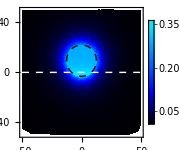
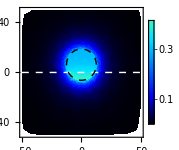
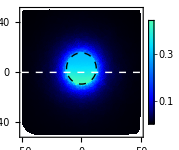
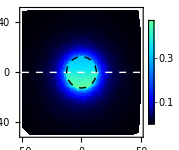
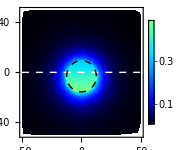
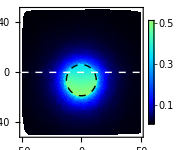
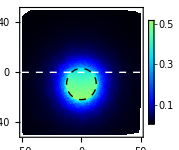

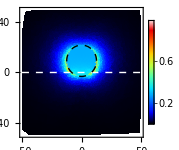

```mathematica
case = Table[i,{i,.75,-.75,-.25}];
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]}&/@case;

plotsX = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
plotsY = MapThread[ListDensityPlot[#1,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}]
```

Far Field (Normal X, All WaveLengths)

```mathematica
cases = {7,6,5,1,2,3,4};
```

```mathematica
data =  FileNames["3*","Normal"]; 
data = data[[#]]&/@cases;
data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
```

Normal/3-Abs-FarX-p75.csv
Normal/3-Abs-FarX-p50.csv
Normal/3-Abs-FarX-p25.csv
Normal/3-Abs-FarX-00.csv
Normal/3-Abs-FarX-m25.csv
Normal/3-Abs-FarX-m50.csv
Normal/3-Abs-FarX-m75.csv

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={Red,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
max = Max[#[[;;,;;,2]]]&/@data;
max = Max[max]
case = Table[i,{i,.75,-.75,-.25}];

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
PlotStyle->#3,
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],LightYellow,Disk[1*{0,max*#2}/3.5,max /3.5]},
Epilog->arrows[Pi/2,max*1.1]
]&,
{data,case,colors[[;;Length[data]]]}]



prol = MapThread[{Opacity[.5],#2,Disk[1*{0,max*#1}/3.5,max /3.5] }&,{case,colors[[;;Length[data]]]}];

ListPolarPlot[data/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
PlotStyle->colors,
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->Flatten[{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],prol}],
Epilog->arrows[Pi/2,max*1.1]
]
```

2.16377

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

Far Field (Normal Y, All WaveLengths)

```mathematica
cases = {7,6,5,1,2,3,4};
```

```mathematica
data =  FileNames["4*","Normal"]; 
data = data[[#]]&/@cases;
data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
```

Normal/4-Abs-FarY-p75.csv
Normal/4-Abs-FarY-p50.csv
Normal/4-Abs-FarY-p25.csv
Normal/4-Abs-FarY-00.csv
Normal/4-Abs-FarY-m25.csv
Normal/4-Abs-FarY-m50.csv
Normal/4-Abs-FarY-m75.csv

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={Red,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
max = Max[#[[;;,;;,2]]]&/@data;
max = Max[max]
case = Table[i,{i,.75,-.75,-.25}];

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
PlotStyle->#3,
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],LightYellow,Disk[1*{0,max*#2}/3.5,max /3.5]},
Epilog->arrows[Pi/2,max*1.1]
]&,
{data,case,colors[[;;Length[data]]]}]



prol = MapThread[{Opacity[.5],#2,Disk[1*{0,max*#1}/3.5,max /3.5] }&,{case,colors[[;;Length[data]]]}];

ListPolarPlot[data/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
PlotStyle->colors,
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->Flatten[{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],prol}],
Epilog->arrows[Pi/2,max*1.1]
]
```

2.16377

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-